# An Elementary Introduction to Wolfram Language

## Part 1

## 列表

点图、折线图和条形图

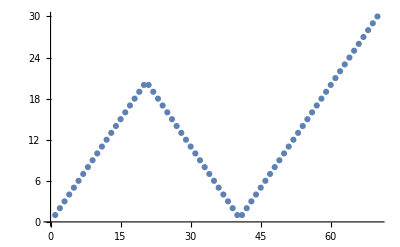

```mathematica
ListPlot[Join[Range@20,Reverse@Range@20,Range@30]]
```

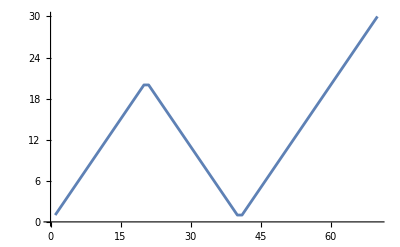

```mathematica
ListLinePlot[Join[Range@20,Reverse@Range@20,Range@30]]
```

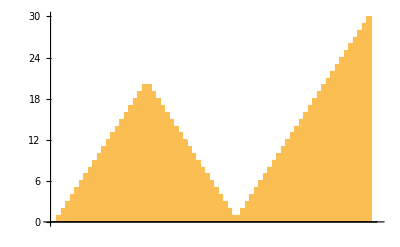

```mathematica
BarChart[Join[Range@20,Reverse@Range@20,Range@30]]
```

饼图

```mathematica
Table[PieChart[Table[1,n]],{n,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

展示阿尔伯特·爱因斯坦不平凡的公民身份的历史变迁：

```mathematica
data={{Interval[{1879,1896}],"Kingdom of Württemberg - German Empire"},{Interval[{1896,1901}],"Stateless"},{Interval[{1901,1955}],"Switzerland"},{Interval[{1911,1912}],"Austria - Austro-Hungarian Empire"},{Interval[{1914,1918}],"Kingdom of Prussia - German Empire"},{Interval[{1918,1933}],"Free State of Prussia - Weimar Republic"},{Interval[{1940,1955}],"United States"}};
```

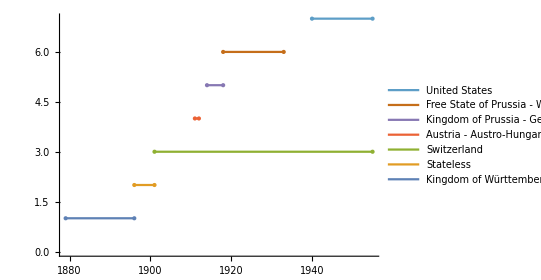

```mathematica
NumberLinePlot[data[[All,1]],PlotLegends->data[[All,-1]],AspectRatio->.7]
```

## 颜色和样式

随机颜色和尺寸

```mathematica
Table[Style[x,RandomColor[],RandomInteger[30]],25]
```

{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}

## 基本图形对象

多边形

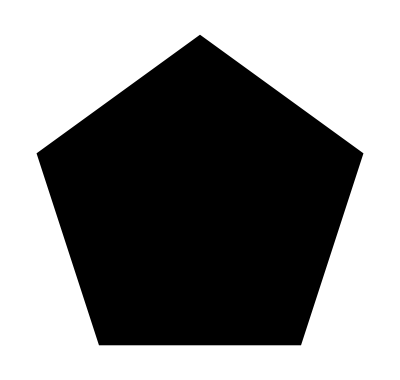
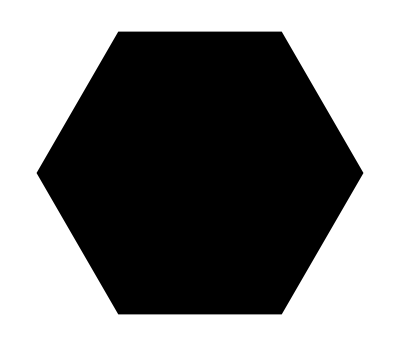
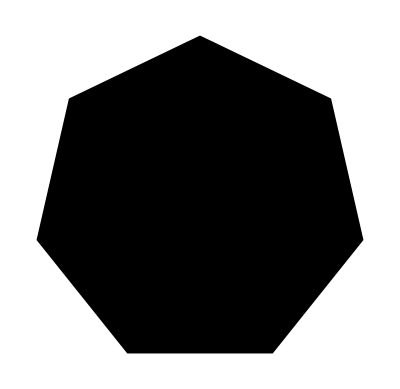
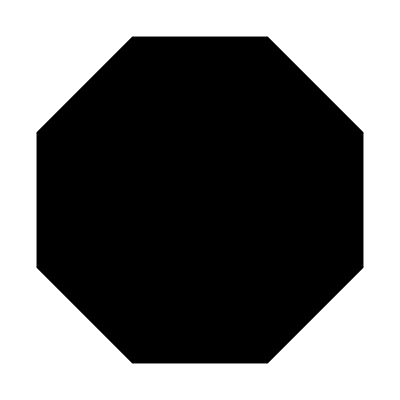
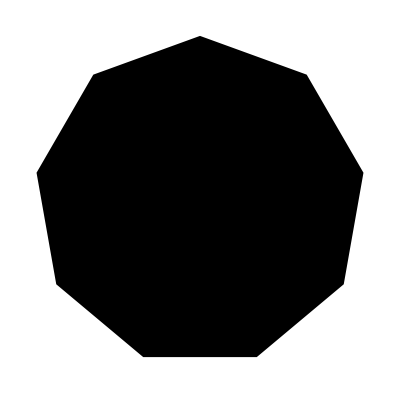
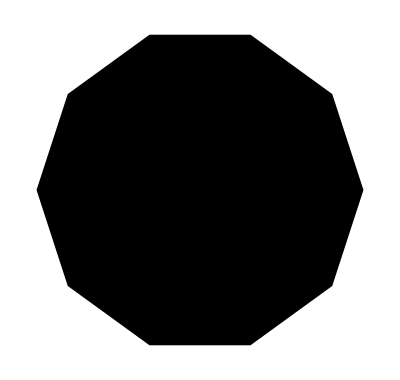

```mathematica
Table[Graphics@RegularPolygon[n],{n,5,10}]
```

计算图形面积和周长

```mathematica
Area/@Table[RegularPolygon[n],{n,5,10}]
```

{5/4 √(1/2 (5+√5)),(3 √3)/2,7/2 Cos[(3 π)/14],2 √2,9/2 Sin[(2 π)/9],5/2 √(1/2 (5-√5))}

```mathematica
Perimeter/@Table[RegularPolygon[n],{n,5,10}]
```

{10 √(5/8-(√5)/8),6,14 Sin[π/7],16 Sin[π/8],18 Sin[π/9],5 (-1+√5)}

圆锥和圆柱

```mathematica
Graphics3D/@{Cone[],Cylinder[]}
```

{-Graphics3D-,-Graphics3D-}

计算图形体积和表面积

```mathematica
Volume/@{Cone[],Cylinder[]}
```

{(2 π)/3,2 π}

```mathematica
SurfaceArea/@{Cone[],Cylinder[]}
```

{(1+√5) π,6 π}

## 交互式操作

由于语法的一致性，很容易将上面的Table改为Manipulate

```mathematica
Manipulate[PieChart[Table[1,n]],{n,1,15,1}]
```

```mathematica
Manipulate[Graphics@Style[RegularPolygon[n],color],{n,5,20,1},{color,{Red,Yellow,Blue}}]
```

## 图像

一定要运行

```mathematica
CurrentImage[]
```

```mathematica
img=-Graphics-;
```

给出图像中主要颜色

```mathematica
DominantColors[img]
```

{RGBColor[0.7554064653460433, 0.7408577908892661, 0.7645094293984959, 1.],RGBColor[0.052775252553601264, 0.040851224965664505, 0.04089094635719579, 1.],RGBColor[0.20564709483290816, 0.18209649478523096, 0.09124042507738217, 1.],RGBColor[0.3565633961627031, 0.40013829112087357, 0.5105967955658899, 1.],RGBColor[0.15725274193972485, 0.20295072324552993, 0.3005475960706814, 1.],RGBColor[0.261915289064134, 0.040359455604079324, 0.04973010310692965, 1.],RGBColor[0.5865463227136153, 0.2354057577574501, 0.16484444370900464, 1.]}

二值化

```mathematica
Manipulate[Binarize[img,t],{t,0,1},ContentSize->{240, 230}]
```

二值化后主色当然为黑白

```mathematica
DominantColors@Binarize@img
```

{RGBColor[0., 0., 0.],RGBColor[0.9999999999999997, 1., 0.9999999999999999]}

各种操作

```mathematica
Through[{Blur[#,10]&,ColorNegate,EdgeDetect,ImageAdd[#,EdgeDetect@#]&}[img]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}